```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX

## Vegas Grids

```mathematica
nrfiles=10;
nrbins=100;
```

```mathematica
Grids=Table[Get["VegasGrids/Step"<>ToString[i]<>".txt"],{i,1,nrfiles}];
```

```mathematica
Grids2=Table[Table[Mean/@Grids[[i,j]],{j,1,Length[Grids[[i]]]}],{i,1,Length[Grids]}];
```

```mathematica
Grids3=Table[Table[1/(#[[2]]-#[[1]])&/@Grids[[i,j]],{j,1,Length[Grids[[i]]]}],{i,1,Length[Grids]}];
```

```mathematica
Grids2//Dimensions
```

{10,3,100}

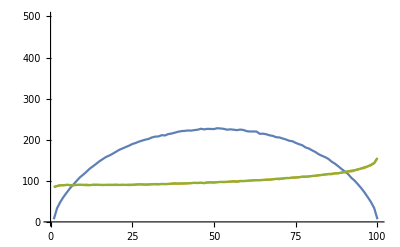

```mathematica
pos=nrfiles;
ListLinePlot[{Grids3[[pos,1]],Grids3[[pos,2]],Grids3[[pos,3]]},PlotRange->{0,500}]
```

### Y=a x+c

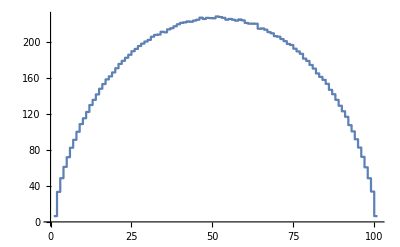

```mathematica
ListStepPlot[Grids3[[pos,1]]]
```

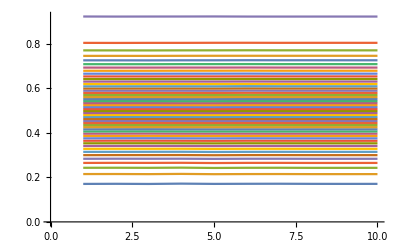

```mathematica
var=1;
ListLinePlot[Table[Grids2[[;;,var,2i]],{i,1,nrbins/2}]]
```

### x1

```mathematica
Mean[Grids3[[pos,2]]]
Grids3[[pos,2]][[64]]
```

101.615

101.814

```mathematica
Total[Grids3[[pos,2]][[57;;]]]/Total[Grids3[[pos,2]]]
```

0.492569

```mathematica
0.43^4
```

0.034188

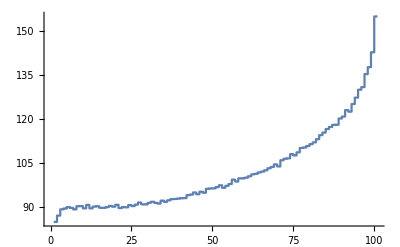

```mathematica
ListStepPlot[Grids3[[pos,2]]]
```

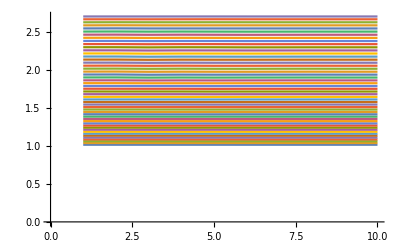

```mathematica
var=2;
ListLinePlot[Table[Exp/@Grids2[[;;,var,2i]],{i,1,nrbins/2}]]
```

### x2

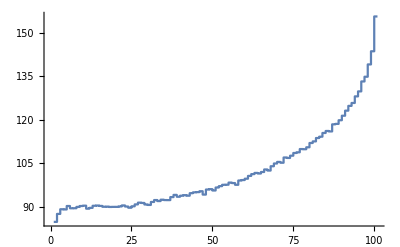

```mathematica
ListStepPlot[Grids3[[pos,3]],PlotRange->All]
```

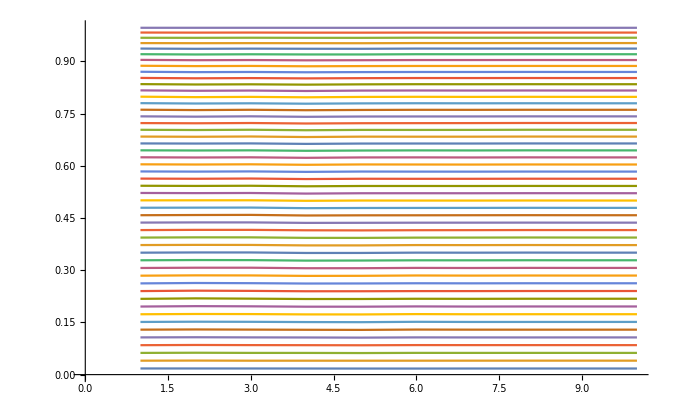

```mathematica
var=3;
ListLinePlot[Table[Grids2[[;;,var,2i]],{i,1,nrbins/2}]]
```